# Single-shot Readout for Superconducting Qubit w/ Two-tone Readout & Shelving Techniques

```mathematica
myred=ColorData[97][4];myblue=ColorData[97][1];myorange=ColorData[97][2];mygreen=ColorData[97][3];
save="C:\\Users\\Leon\\Pictures\\Purcell\\vectorPlot\\";
dataPath="https://raw.githubusercontent.com/muxueqianxun/SuperconductingQubitReadout/main/ReadoutData/";
fontsize=18;font="CMU Sans Serif";
SetOptions[EvaluationNotebook[],StyleDefinitions->Cell[StyleData["GraphicsLabel"],Black,fontsize,FontFamily->font]];
```

## Single-shot Readout IQ Data

### Import IQ Data

```mathematica
dataPathIQ=dataPath<>"IQ/";
calib1i=Flatten[Import[dataPathIQ<>"t1i_gefh_calib.csv","csv"]];
calib1q=Flatten[Import[dataPathIQ<>"t1q_gefh_calib.csv","csv"]];
calib2i=Flatten[Import[dataPathIQ<>"t2i_gefh_calib.csv","csv"]];
calib2q=Flatten[Import[dataPathIQ<>"t2q_gefh_calib.csv","csv"]];
data1i=Flatten[Import[dataPathIQ<>"t1i_gef_data.csv","csv"]];
data1q=Flatten[Import[dataPathIQ<>"t1q_gef_data.csv","csv"]];
data2i=Flatten[Import[dataPathIQ<>"t2i_gef_data.csv","csv"]];
data2q=Flatten[Import[dataPathIQ<>"t2q_gef_data.csv","csv"]];
data1ipre=Flatten[Import[dataPathIQ<>"t1i_gef_data_pre.csv","csv"]];
data1qpre=Flatten[Import[dataPathIQ<>"t1q_gef_data_pre.csv","csv"]];
data2ipre=Flatten[Import[dataPathIQ<>"t2i_gef_data_pre.csv","csv"]];
data2qpre=Flatten[Import[dataPathIQ<>"t2q_gef_data_pre.csv","csv"]];
```

### Sample Training Data

```mathematica
calibAll={calib1i,calib1q,calib2i,calib2q}ᵀ;
dataAll={data1i,data1q,data2i,data2q}ᵀ;
preData={data1ipre,data1qpre,data2ipre,data2qpre}ᵀ;
dataLen=Dimensions[calibAll]⟦1⟧/4;
dataGpre=preData⟦1;;1*dataLen⟧;
dataEpre=preData⟦dataLen+1;;2*dataLen⟧;
dataFpre=preData⟦2*dataLen+1;;3*dataLen⟧;
dataG=dataAll⟦1;;1*dataLen⟧;
dataE=dataAll⟦dataLen+1;;2*dataLen⟧;
dataF=dataAll⟦2*dataLen+1;;3*dataLen⟧;
calibG=calibAll⟦1;;1*dataLen⟧;
calibE=calibAll⟦dataLen+1;;2*dataLen⟧;
calibF=calibAll⟦2*dataLen+1;;3*dataLen⟧;
calibH=calibAll⟦3*dataLen+1;;4*dataLen⟧;
sample=10000;
calibGSample=RandomSample[calibG,sample];
calibESample=RandomSample[calibE,sample];
calibFSample=RandomSample[calibF,sample];
calibHSample=RandomSample[calibH,sample];
```

### Plot IQ Values

#### Primary Tone

```mathematica
dataGMeant1=Mean[calibG]⟦1;;2⟧;
dataEMeant1=Mean[calibE]⟦1;;2⟧;
dataFMeant1=Mean[calibF]⟦1;;2⟧;
datat1=Mean[{dataGMeant1,dataEMeant1}];
```

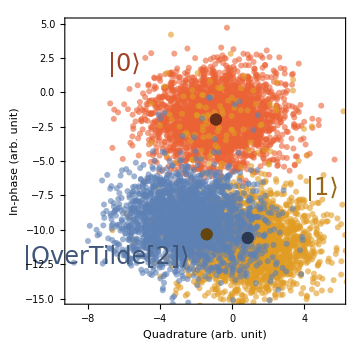

```mathematica
sample1=2500;
dataGSamplet1=RandomSample[dataG,sample1]⟦All,1;;2⟧;
dataESamplet1=RandomSample[dataE,sample1]⟦All,1;;2⟧;
dataFSamplet1=RandomSample[dataF,sample1]⟦All,1;;2⟧;
pts=0.012;opa=0.6;
rt1=Show[ListPlot[{dataGSamplet1,dataFSamplet1,dataESamplet1},PlotStyle->{{PointSize[pts],myred,Opacity[opa]}(*,{PointSize[pts],mygreen,Opacity[opa]}*),{PointSize[pts],myorange,Opacity[opa]},{PointSize[pts],myblue,Opacity[opa]}},Joined->False,AspectRatio->1,Frame->True,Axes->False,FrameLabel->{{"In-phase (arb. unit)"(*""*),""},{"Quadrature (arb. unit)","Secondary Tone\nReadout Reponse"}},ImageSize->Medium,PlotRange->{{-9,6},{-15,5}},Epilog->{{Text[Style["|0⟩",24,Darker[myred]],{-6,2}]},{Text[Style["|OverTilde[2]⟩",24,Darker[myblue]],{-7,-12}]},{Text[Style["|1⟩",24,Darker[myorange]],{5,-7}]}}],
ListPlot[{{dataGMeant1},{dataEMeant1},{dataFMeant1}(*{dataFMean1},{dataHMean1}*)},PlotStyle->{{PointSize[2*pts],Darker[Darker[myred]]}(*,{PointSize[2*pts],Darker[Darker[mygreen]]}*),{PointSize[2*pts],Darker[Darker[myblue]]},{PointSize[2*pts],Darker[Darker[myorange]]}}]]
```

#### Secondary Tone

```mathematica
dataGMeant2=Mean[dataG]⟦3;;4⟧;
dataEMeant2=Mean[dataE]⟦3;;4⟧;
dataFMeant2=Mean[dataF]⟦3;;4⟧;
datat2=Mean[{dataGMeant2,dataEMeant2,dataFMeant2}];
```

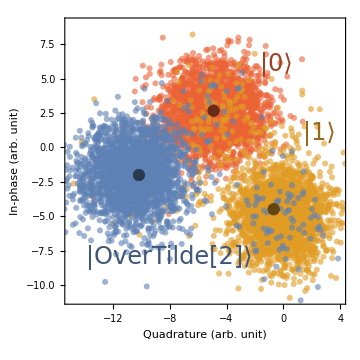

```mathematica
sample1=2500;
dataGSample1=RandomSample[dataG,sample1]⟦All,3;;4⟧;
dataESample1=RandomSample[dataE,sample1]⟦All,3;;4⟧;
dataFSample1=RandomSample[dataF,sample1]⟦All,3;;4⟧;
pts=0.012;opa=0.6;
rt2=Show[ListPlot[{dataGSample1,dataFSample1,dataESample1},PlotStyle->{{PointSize[pts],myred,Opacity[opa]}(*,{PointSize[pts],mygreen,Opacity[opa]}*),{PointSize[pts],myorange,Opacity[opa]},{PointSize[pts],myblue,Opacity[opa]}},Joined->False,AspectRatio->1,Frame->True,Axes->False,FrameLabel->{{"In-phase (arb. unit)"(*""*),""},{"Quadrature (arb. unit)","Secondary Tone\nReadout Reponse"}},ImageSize->Medium,PlotRange->{{-15,4},{9-20,9}},Epilog->{{Text[Style["|0⟩",24,Darker[myred]],{-0.5,6}]},{Text[Style["|OverTilde[2]⟩",24,Darker[myblue]],{-8,-8}]},{Text[Style["|1⟩",24,Darker[myorange]],{2.5,1}]}}],
ListPlot[{{dataGMeant2},{dataEMeant2},{dataFMeant2}(*{dataFMean1},{dataHMean1}*)},PlotStyle->{{PointSize[2*pts],Darker[Darker[myred]]}(*,{PointSize[2*pts],Darker[Darker[mygreen]]}*),{PointSize[2*pts],Darker[Darker[myblue]]},{PointSize[2*pts],Darker[Darker[myorange]]}}]]
```

## Baseline Single-tone Assignment Fidelity

```mathematica
Clear[PointerState]
PointerState[meanList_,data_]:=Module[{},distance={};
Do[AppendTo[distance,
Norm[#-meanList⟦i⟧]&/@data],{i,1,Dimensions[meanList]⟦-1⟧+1}];
count=Position[#,Min[#]]⟦1,1⟧&/@(distanceᵀ);
count]
```

### Pointer-state Classification

```mathematica
calibGMean=Mean[calibG]⟦3;;4⟧;
calibEMean=Mean[calibE]⟦3;;4⟧;
calibFMean=Mean[calibF]⟦3;;4⟧;
```

```mathematica
meanList={calibGMean,calibEMean,calibFMean};
count=PointerState[meanList,calibAll⟦;;-dataLen,3;;4⟧]-1;
```

### Re-construct and Plot Assignment Matrix

```mathematica
select= Table[True,dataLen*3];
cms=FindCM[Partition[count,dataLen],Partition[select,dataLen],Partition[preSelect,dataLen],plot=True,twotone=False];
```

```mathematica
m=Round[cms⟦2⟧*100,0.01];
a=50;max=100;
cf=Opacity[1-a^(-#/max),myblue]&;
fa=Round[Mean[Diagonal[cms⟦2⟧*100]],0.01];
t=Transpose@Map[Flatten,{#,Reverse@Transpose@#}&[Table[Range[1,2 #-1,2],{#}]]&[Length@m]]/2;
```

```mathematica
ml=Round[cms⟦2⟧*100,100];
legendPlot=Show[MatrixPlot[ml,(*ImageMargins->{{20,0},{0,20}},*)ImageSize->{120,350},ColorFunction->cf,ColorFunctionScaling->False,BaseStyle->{FontFamily->font},PlotLegends-> Placed[BarLegend[Automatic,LegendMarkerSize->250,LegendLabel->Placed[Style["Assignment Probability (%)",FontSize->fontsize,FontFamily->font],Right,Rotate[#,90 Degree]&]],{1,0.5}]],MatrixPlot[ml,Epilog->Style[Text@@@Transpose[{Catenate@ml,t}],fontsize,Black],FrameTicks->{{{1,"|0⟩"},{2,"|1⟩"},{3,"|2⟩"}},{{1,"|0⟩"},{2,"|1⟩"},{3,"|2⟩"}}},ImageSize->350,ColorFunction->cf,ColorFunctionScaling->False]];
cm0Plot=Show[MatrixPlot[m,Epilog->MapIndexed[Text[Style[Round[#,.01],fontsize,If[Abs[#]≥50,White,Black],FontFamily->font],{#2[[2]],4-#2[[1]]}-.5]&,m,{2}],(*ImageMargins->{{20,0},{0,20}},*)FrameTicks->{{{1,"|0⟩"},{2,"|1⟩"},{3,"|2⟩"}},{{1,"|0⟩"},{2,"|1⟩"},{3,"|2⟩"}}},ImageSize->{460,350},ColorFunction->cf,ColorFunctionScaling->False,BaseStyle->{FontFamily->font},(*PlotLegends-> Placed[BarLegend[Automatic,LegendMarkerSize->200,LegendLabel->Placed[Style["Assignment Probability (%)",FontSize->24],Right,Rotate[#,90 Degree]&]],{1,0.5}],*)FrameLabel->{ "Prepared State","Measured State","",Style["Three-state Readout\n Assignment Fidelity ℱ_a = "<>ToString[fa]<>"%",fontsize]}],MatrixPlot[m,Epilog->Style[Text@@@Transpose[{Catenate@m,t}],fontsize,Black],FrameTicks->{{{1,"|0⟩"},{2,"|1⟩"},{3,"|2⟩"}},{{1,"|0⟩"},{2,"|1⟩"},{3,"|2⟩"}}},ImageSize->352,ColorFunction->cf,ColorFunctionScaling->False]];
Show[cm0Plot,legendPlot]
```

-Graphics-

## Neural Network

### Train Neural Network

```mathematica
trainingData=Flatten[{#-> 0&/@calibGSample,#-> 1&/@calibESample,#-> 3&/@calibHSample}];
net=NetChain[{LinearLayer[32],ElementwiseLayer[Ramp],LinearLayer[3],SoftmaxLayer[]},"Input"->{4},"Output"->NetDecoder[{"Class",{0,1,3}}]];
Information[net,"SummaryGraphic"]
```

-Graphics-

```mathematica
results=NetTrain[net,trainingData,All]
trained=results["TrainedNet"]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:12194  rounds:26  time:28s  examples/s:28234
data | ,,  training examples:30000  processed examples:780416  skipped examples:0
method | ,,  ADAMoptimizer  batch size64CPU
round | ,,  loss:1.51×10^-1  error:3.26%
 | 
 | ]

NetChain[<>]

## State Discrimination

```mathematica
Clear[ThresholdData,FindCM] 
ThresholdData[countProb_,thres_]:=Module[{},gselect=(Max[#]>thres⟦1⟧)&/@(Flatten[Values[countProb⟦1⟧]]);
eselect=(Max[#]>thres⟦2⟧)&/@(Flatten[Values[countProb⟦2⟧]]);
fselect=(Max[#]>thres⟦3⟧)&/@(Flatten[Values[countProb⟦3⟧]]);
{gselect,eselect,fselect}]
FindCM[count_,select_,preselect_,plot_:False,twotone_:True]:=Module[{},gselectFinal=Thread[And[select⟦1⟧,preselect⟦1⟧]];
eselectFinal=Thread[And[select⟦2⟧,preselect⟦2⟧]];
fselectFinal=Thread[And[select⟦3⟧,preselect⟦3⟧]];
gcountFinal=Pick[count⟦1⟧,gselectFinal];ecountFinal=Pick[count⟦2⟧,eselectFinal];fcountFinal=Pick[count⟦3⟧,fselectFinal];
If[twotone,
cag=Flatten[Count[gcountFinal,#](*/Dimensions[gcountFinal]*)&/@{0,1,2,3}];
cag=cag⟦1;;2⟧~Join~{Total[cag⟦3;;4⟧]}//N;
cae=Flatten[Count[ecountFinal,#](*/Dimensions[ecountFinal]*)&/@{0,1,2,3}];
cae={cae⟦1⟧}~Join~{Total[cae⟦3;;4⟧]}~Join~{cae⟦2⟧}//N;
caf=Flatten[Count[fcountFinal,#](*/Dimensions[fcountFinal]*)&/@{0,1,2,3}];
caf={caf⟦1⟧}~Join~{Total[caf⟦3;;4⟧]}~Join~{caf⟦2⟧}//N;
,
cag=Flatten[Count[gcountFinal,#](*/Dimensions[gcountFinal]*)&/@{0,1,2}];
cae=Flatten[Count[ecountFinal,#](*/Dimensions[ecountFinal]*)&/@{0,1,2}];
caf=Flatten[Count[fcountFinal,#](*/Dimensions[fcountFinal]*)&/@{0,1,2}];];
cm={cag,cae,caf};
cmNorm={cag/Dimensions[gcountFinal]⟦1⟧,cae/Dimensions[ecountFinal]⟦1⟧,caf/Dimensions[fcountFinal]⟦1⟧};
(*If[plot,
Print[Mean[Diagonal[cm]],cm//MatrixForm,Mean[Diagonal[cmNorm]],cmNorm//MatrixForm]];*)
{cm,cmNorm}]
```

### Preselection

```mathematica
c=trained;
gprecountProb=c[dataGpre,"Probabilities"];
eprecountProb=c[dataEpre,"Probabilities"];
fprecountProb=c[dataFpre,"Probabilities"];
```

```mathematica
threspre=0.5;
gpreselect=(#>threspre)&/@(0/.gprecountProb);
epreselect=(#>threspre)&/@(0/.eprecountProb);
fpreselect=(#>threspre)&/@(0/.fprecountProb);
preselect={gpreselect,epreselect,fpreselect};
```

### Classification

```mathematica
gcountProb=MaximalBy[1]@# &/@c[dataG,"Probabilities"];
ecountProb=MaximalBy[1]@# &/@c[dataE,"Probabilities"];
fcountProb=MaximalBy[1]@# &/@c[dataF,"Probabilities"];
gcount=Flatten[Keys[gcountProb]];ecount=Flatten[Keys[ecountProb]];fcount=Flatten[Keys[fcountProb]];
countProb ={gcountProb,ecountProb,fcountProb};
count = {gcount,ecount,fcount};
```

### Optimize Confidence Thresholds

```mathematica
thresSweep=Range[0.8,0.99,0.005];
cmList={};cmfList={};
Do[thres=thresSweep⟦i⟧;
select=ThresholdData[countProb,Table[thres,3]];
cms=FindCM[count,select,preselect];
AppendTo[cmList,cms⟦1⟧];
AppendTo[cmfList,cms⟦2⟧];
,{i,1,Dimensions[thresSweep]⟦1⟧}]
```

```mathematica
cmPlotList={};thresList={};cutoff=0.9;
Do[cmMax=Max[#]&/@(cmList⟦All,i⟧ᵀ);
cmPlot={Table[thresSweep,3],cmList⟦All,i⟧ᵀ/cmMax}ᵀ;
cmPlot=#ᵀ&/@cmPlot;cmPlot⟦i⟧;
thresIdx=Nearest[cmPlot⟦i⟧⟦All,2⟧-> "Index",cutoff];
thresPt=thresSweep⟦thresIdx⟦1⟧⟧;
AppendTo[cmPlotList,cmPlot];AppendTo[thresList,thresPt];
(*Print[ListPlot[cmPlot,Joined->True,PlotRange-> {0.7,1}]];*)
,{i,1,3}]
```

### Re-construct Assignment Matrix

```mathematica
select=ThresholdData[countProb,thresList];
cms=FindCM[count,select,preselect,plot=True];
```

```mathematica
m=Round[cms⟦2⟧*100,0.01];
a=50;max=100;
cf=Opacity[1-a^(-#/max),myblue]&;
fa=Round[Mean[Diagonal[cms⟦2⟧*100]],0.01];
t=Transpose@Map[Flatten,{#,Reverse@Transpose@#}&[Table[Range[1,2 #-1,2],{#}]]&[Length@m]]/2;
```

```mathematica
ml=Round[cms⟦2⟧*100,100];
legendPlot=Show[MatrixPlot[ml,(*ImageMargins->{{20,0},{0,20}},*)ImageSize->{120,350},ColorFunction->cf,ColorFunctionScaling->False,BaseStyle->{FontFamily->font},PlotLegends-> Placed[BarLegend[Automatic,LegendMarkerSize->250,LegendLabel->Placed[Style["Assignment Probability (%)",FontSize->fontsize,FontFamily->font],Right,Rotate[#,90 Degree]&]],{1,0.5}]],MatrixPlot[ml,Epilog->Style[Text@@@Transpose[{Catenate@ml,t}],fontsize,Black],FrameTicks->{{{1,"|0⟩"},{2,"|1⟩"},{3,"|2⟩"}},{{1,"|0⟩"},{2,"|1⟩"},{3,"|2⟩"}}},ImageSize->350,ColorFunction->cf,ColorFunctionScaling->False]];
cm0Plot=Show[MatrixPlot[m,Epilog->MapIndexed[Text[Style[Round[#,.01],fontsize,If[Abs[#]≥50,White,Black],FontFamily->font],{#2[[2]],4-#2[[1]]}-.5]&,m,{2}],(*ImageMargins->{{20,0},{0,20}},*)FrameTicks->{{{1,"|0⟩"},{2,"|1⟩"},{3,"|2⟩"}},{{1,"|0⟩"},{2,"|1⟩"},{3,"|2⟩"}}},ImageSize->{460,350},ColorFunction->cf,ColorFunctionScaling->False,BaseStyle->{FontFamily->font},(*PlotLegends-> Placed[BarLegend[Automatic,LegendMarkerSize->200,LegendLabel->Placed[Style["Assignment Probability (%)",FontSize->24],Right,Rotate[#,90 Degree]&]],{1,0.5}],*)FrameLabel->{ "Prepared State","Measured State","",Style["Three-state Readout\n Assignment Fidelity ℱ_a = "<>ToString[fa]<>"%",fontsize]}],MatrixPlot[m,Epilog->Style[Text@@@Transpose[{Catenate@m,t}],fontsize,Black],FrameTicks->{{{1,"|0⟩"},{2,"|1⟩"},{3,"|2⟩"}},{{1,"|0⟩"},{2,"|1⟩"},{3,"|2⟩"}}},ImageSize->352,ColorFunction->cf,ColorFunctionScaling->False]];
Show[cm0Plot,legendPlot]
```

-Graphics-

### Plot Decision Boundary

#### Primary Tone

```mathematica
x1=-9;x2=6;y1=-15;y2=5;
xy1=Table[{i,j},{i,x1,x2},{j,y1,y2}];
d=Dimensions[xy1];
myPiecewise[x_]:=Piecewise[{{Directive[myred,Opacity[0.1]],0≤x<1},{Transparent,1≤x<2}}]
cp11=ContourPlot[c[{x,y,datat2⟦1⟧,datat2⟦2⟧}]/.{2->1,3->1},{x,x1,x2},{y,y1,y2},ColorFunction->myPiecewise,ColorFunctionScaling->False,ContourStyle->Directive[Black,0.01,Dashed],Contours->1];
myPiecewise[x_]:=Piecewise[{{Transparent,0≤x<1},{Directive[myblue,Opacity[0.1]],1≤x<2}}]
cp41=ContourPlot[c[{x,y,datat2⟦1⟧,datat2⟦2⟧}]/.{1->1,2->1,3->1},{x,x1,x2},{y,y1,y2},ColorFunction->myPiecewise,ColorFunctionScaling->False,ContourStyle->Directive[Black,0.01,Dashed],Contours->1];
dbt1=Show[cp11,cp41];
```

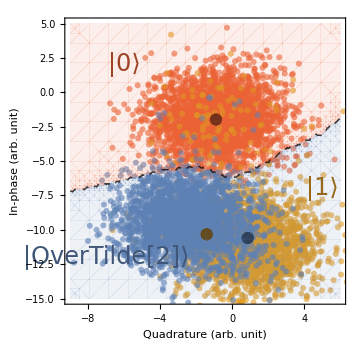

```mathematica
Show[rt1,dbt1]
```

#### Secondary Tone

```mathematica
x1=-20;x2=5;y1=-15;y2=10;
xy1=Table[{i,j},{i,x1,x2},{j,y1,y2}];
d=Dimensions[xy1];
myPiecewise[x_]:=Piecewise[{{Directive[myred,Opacity[0.1]],0≤x<1},{Transparent,1≤x<2}}]
cp11=ContourPlot[c[{datat1⟦1⟧,datat1⟦2⟧,x,y}]/.{2->1,3->1},{x,x1,x2},{y,y1,y2},ColorFunction->myPiecewise,ColorFunctionScaling->False,ContourStyle->Directive[Black,0.01,Dashed],Contours->1];
myPiecewise[x_]:=Piecewise[{{Transparent,0≤x<1},{Directive[myorange,Opacity[0.1]],1≤x<2}}]
cp21=ContourPlot[c[{datat1⟦1⟧,datat1⟦2⟧,x,y}]/.{2->0,3->0},{x,x1,x2},{y,y1,y2},ColorFunction->myPiecewise,ColorFunctionScaling->False,ContourStyle->Directive[Black,0.01,Dashed],Contours->1];
myPiecewise[x_]:=Piecewise[{{Transparent,0≤x<1},{Directive[myblue,Opacity[0.1]],1≤x<2}}]
cp41=ContourPlot[c[{datat1⟦1⟧,datat1⟦2⟧,x,y}]/.{1->0,2->0,3->1},{x,x1,x2},{y,y1,y2},ColorFunction->myPiecewise,ColorFunctionScaling->False,ContourStyle->Directive[Black,0.01,Dashed],Contours->1];
dbt2=Show[cp11,cp21,cp41];
```

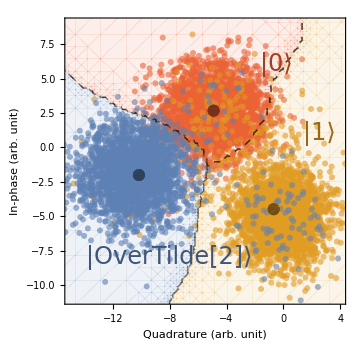

```mathematica
Show[rt2,dbt2]
```